```mathematica
Clear[a,b,w,f,g,g1,g2,g3,g4,x,y,z,p]
```

```mathematica
(*WHITCOMB INTEGRAL SUPERCRITICAL AIRFOIL*)
```

```mathematica
(*top*)
```

```mathematica
a={{0.0 ,0.0},

{.0075 ,.0176},

{.0125, .0215},

{.0250 ,.0276},

{.0375 ,.0316},

{.0500 ,.0347},

{.0750 ,.0394},

{.1000 ,.0428},

{.1250 ,.0455},

{.1500 ,.0476},

{.1750, .0493},

{.2000 ,.0507},

{.2500, .0528},

{.3000, .0540},

{.3500 ,.0547},

{.4000 ,.0550},

{.4500, .0548},

{.5000, .0543},

{.5500, .0533},

{.5750, .0527},

{.6000 ,.0519},

{.6250 ,.0511},

{.6500 ,.0501},

{.6750 ,.0489},

{.7000, .0476},

{.7250 ,.0460},

{.7500 ,.0442},

{.7750 ,.0422},

{.8000 ,.0398},

{.8250 ,.0370},

{.8500 ,.0337},

{.8750 ,.0300},

{.9000 ,.0255},

{.9250 ,.0204},

{.9500, .0144},

{.9750 ,.0074},

{1.0000,.0008},{1.0075,0}}
```

{{0.,0.},{0.0075,0.0176},{0.0125,0.0215},{0.025,0.0276},{0.0375,0.0316},{0.05,0.0347},{0.075,0.0394},{0.1,0.0428},{0.125,0.0455},{0.15,0.0476},{0.175,0.0493},{0.2,0.0507},{0.25,0.0528},{0.3,0.054},{0.35,0.0547},{0.4,0.055},{0.45,0.0548},{0.5,0.0543},{0.55,0.0533},{0.575,0.0527},{0.6,0.0519},{0.625,0.0511},{0.65,0.0501},{0.675,0.0489},{0.7,0.0476},{0.725,0.046},{0.75,0.0442},{0.775,0.0422},{0.8,0.0398},{0.825,0.037},{0.85,0.0337},{0.875,0.03},{0.9,0.0255},{0.925,0.0204},{0.95,0.0144},{0.975,0.0074},{1.,0.0008},{1.0075,0}}

```mathematica
Length[a]
```

38

```mathematica
f[x_]=Fit[a,Table[x^n,{n,0,Length[a]}],x]
```

0.000269654+3.14532 x-160.2 x^2+4826.68 x^3-88460.4 x^4+1.05158×10^6 x^5-8.48299×10^6 x^6+4.76819×10^7 x^7-1.88434×10^8 x^8+5.1734×10^8 x^9-9.39964×10^8 x^10+9.69318×10^8 x^11-1.84234×10^8 x^12-7.09081×10^8 x^13+3.85782×10^8 x^14+5.91047×10^8 x^15-2.6884×10^8 x^16-6.05634×10^8 x^17-1.56962×10^7 x^18+5.43338×10^8 x^19+3.60968×10^8 x^20-2.4288×10^8 x^21-5.28677×10^8 x^22-2.18698×10^8 x^23+3.07209×10^8 x^24+4.93975×10^8 x^25+1.77353×10^8 x^26-3.07627×10^8 x^27-4.78885×10^8 x^28-1.67449×10^8 x^29+3.17071×10^8 x^30+4.74676×10^8 x^31+1.04553×10^8 x^32-4.16161×10^8 x^33-4.23985×10^8 x^34+2.33897×10^8 x^35+5.81545×10^8 x^36-5.2828×10^8 x^37+1.26287×10^8 x^38

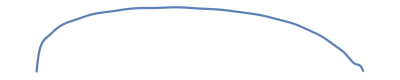

```mathematica
g3=Plot[f[x],{x,0,1},AspectRatio->Automatic,Axes->False]
```

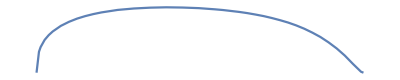

```mathematica
g1=ListLinePlot[a,AspectRatio->Automatic,Axes->False]
```

```mathematica
(*bottom*)
```

```mathematica
b={{0.0 ,0.0},

{.0075,-.0176},

{.0125,-.0216},

{.0250,-.0281},

{.0375,-.0324},

{.0500,-.0358},

{.0750,-.0408},

{.1000,-.0444},

{.1250,-.0472},

{.1500,-.0493},

{.1750,-.0510},

{.2000,-.0522},

{.2500,-.0540},

{.3000,-.0548},

{.3500,-.0549},

{.4000,-.0541},

{.4500,-.0524},

{.5000,-.0497},

{.5500,-.0455},

{.5750,-.0426},

{.6000,-.0389},

{.6250,-.0342},

{.6500,-.0282},

{.6750,-.0215},

{.7000,-.0149},

{.7250,-.0090},

{.7500,-.0036},

{.7750, .0012},

{.8000 ,.0053},

{.8250, .0088},

{.8500 ,.0114},

{.8750, .0132},

{.9000, .0138},

{.9250, .0131},

{.9500, .0106},

{.9750, .0060},

{1.0000,-.0013},{1.0075,0}}
```

{{0.,0.},{0.0075,-0.0176},{0.0125,-0.0216},{0.025,-0.0281},{0.0375,-0.0324},{0.05,-0.0358},{0.075,-0.0408},{0.1,-0.0444},{0.125,-0.0472},{0.15,-0.0493},{0.175,-0.051},{0.2,-0.0522},{0.25,-0.054},{0.3,-0.0548},{0.35,-0.0549},{0.4,-0.0541},{0.45,-0.0524},{0.5,-0.0497},{0.55,-0.0455},{0.575,-0.0426},{0.6,-0.0389},{0.625,-0.0342},{0.65,-0.0282},{0.675,-0.0215},{0.7,-0.0149},{0.725,-0.009},{0.75,-0.0036},{0.775,0.0012},{0.8,0.0053},{0.825,0.0088},{0.85,0.0114},{0.875,0.0132},{0.9,0.0138},{0.925,0.0131},{0.95,0.0106},{0.975,0.006},{1.,-0.0013},{1.0075,0}}

```mathematica
f[x_]=Fit[a,Table[x^n,{n,0,Length[a]}],x]
```

0.000269654+3.14532 x-160.2 x^2+4826.68 x^3-88460.4 x^4+1.05158×10^6 x^5-8.48299×10^6 x^6+4.76819×10^7 x^7-1.88434×10^8 x^8+5.1734×10^8 x^9-9.39964×10^8 x^10+9.69318×10^8 x^11-1.84234×10^8 x^12-7.09081×10^8 x^13+3.85782×10^8 x^14+5.91047×10^8 x^15-2.6884×10^8 x^16-6.05634×10^8 x^17-1.56962×10^7 x^18+5.43338×10^8 x^19+3.60968×10^8 x^20-2.4288×10^8 x^21-5.28677×10^8 x^22-2.18698×10^8 x^23+3.07209×10^8 x^24+4.93975×10^8 x^25+1.77353×10^8 x^26-3.07627×10^8 x^27-4.78885×10^8 x^28-1.67449×10^8 x^29+3.17071×10^8 x^30+4.74676×10^8 x^31+1.04553×10^8 x^32-4.16161×10^8 x^33-4.23985×10^8 x^34+2.33897×10^8 x^35+5.81545×10^8 x^36-5.2828×10^8 x^37+1.26287×10^8 x^38

```mathematica
g3=Plot[f[x],{x,0,1},AspectRatio->Automatic,Axes->False]
```

-Graphics-

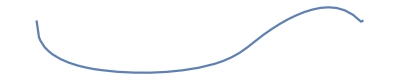

```mathematica
g2=ListLinePlot[b,AspectRatio->Automatic,Axes->False]
```

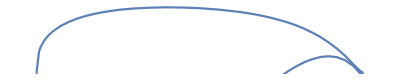

```mathematica
Show[{g1,g2}]
```

```mathematica
Length[b]
```

38

```mathematica
g[x_]=Fit[b,Table[x^n,{n,0,Length[a]}],x]
```

-0.000277621-3.11189 x+154.877 x^2-4614.39 x^3+83750.4 x^4-985563. x^5+7.86501×10^6 x^6-4.36998×10^7 x^7+1.70561×10^8 x^8-4.61923×10^8 x^9+8.26027×10^8 x^10-8.32603×10^8 x^11+1.36812×10^8 x^12+6.17336×10^8 x^13-3.10147×10^8 x^14-5.1325×10^8 x^15+2.08149×10^8 x^16+5.15164×10^8 x^17+3.27619×10^7 x^18-4.48515×10^8 x^19-3.14731×10^8 x^20+1.86997×10^8 x^21+4.39095×10^8 x^22+1.94612×10^8 x^23-2.42466×10^8 x^24-4.09008×10^8 x^25-1.57416×10^8 x^26+2.43659×10^8 x^27+3.94363×10^8 x^28+1.46407×10^8 x^29-2.52351×10^8 x^30-3.89685×10^8 x^31-9.28353×10^7 x^32+3.35336×10^8 x^33+3.49148×10^8 x^34-1.85549×10^8 x^35-4.75153×10^8 x^36+4.27752×10^8 x^37-1.01808×10^8 x^38

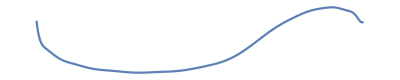

```mathematica
g4=Plot[g[x],{x,0,1},AspectRatio->Automatic,Axes->False]
```

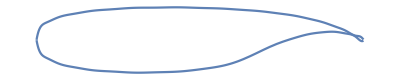

```mathematica
Show[{g3,g4},PlotRange->All]
```

```mathematica
ColorData["GrayYellowTones"]
```

ColorDataFunction[…]

```mathematica
ColorData["PigeonTones"]
```

ColorDataFunction[…]

```mathematica
ColorData["Pastel"]
```

ColorDataFunction[…]

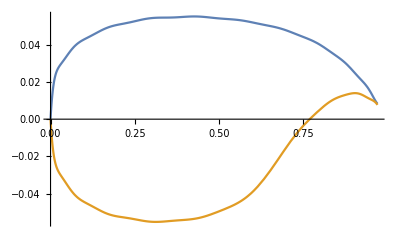

```mathematica
Plot[{f[x],g[x]},{x,0,.97}]
```

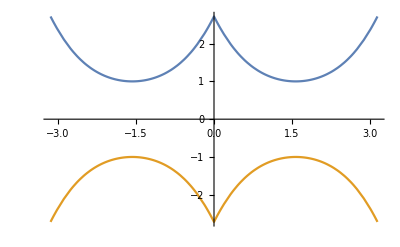

```mathematica
Plot[{Exp[1-Sin[Abs[p]]],-Exp[1-Sin[Abs[p]]]},{p,-Pi,Pi}]
```

```mathematica
gt=ParametricPlot3D[If[x*Cos[p]>=0,{f[x]*Cos[p],x*Cos[p],Exp[1-Sin[Abs[p]]]/2},Nothing],{x,0,0.97},{p,-Pi,Pi},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotPoints->200,ViewPoint->{2,2,2},ColorFunction->"Pastel",Background->LightBlue,ImageSize->2000];
gb=ParametricPlot3D[If[x*Cos[p]>=0,{g[x]*Cos[p],x*Cos[p],Exp[1-Sin[Abs[p]]]/2},Nothing],{x,0,0.97},{p,-Pi,Pi},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotPoints->200,ViewPoint->{2,2,2},ColorFunction->"Pastel",Background->LightBlue,ImageSize->2000];
```

```mathematica
gt1=ParametricPlot3D[If[x*Cos[p]>=0,{f[x]*Cos[p],x*Cos[p],Exp[1]-Exp[1-Sin[Abs[p]]]/2},Nothing],{x,0,0.97},{p,-Pi,Pi},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotPoints->200,ViewPoint->{2,2,2},ColorFunction->"Pastel",Background->LightBlue,ImageSize->2000];
gb1=ParametricPlot3D[If[x*Cos[p]>=0,{g[x]*Cos[p],x*Cos[p],Exp[1]-Exp[1-Sin[Abs[p]]]/2},Nothing],{x,0,0.97},{p,-Pi,Pi},PlotRange->All,Boxed->False,Axes->False,Mesh->None,PlotPoints->200,ViewPoint->{2,2,2},ColorFunction->"Pastel",Background->LightBlue,ImageSize->2000];
```

```mathematica
ga=Show[{gt,gb,gt1,gb1},ImageSize->{2000,2000},ViewPoint->{2,2,2}];
```

```mathematica
Clear[g2,g3,g4]
```

```mathematica
g2=Show[ga,ViewPoint->Front,ImageSize->{2000,2000}];
```

```mathematica
Export["Supercritical_Lifting_Body_Flyingwing_Pastel_g2.jpg",g2]
```

Supercritical_Lifting_Body_Flyingwing_g2.jpg

```mathematica
g3=Show[ga,ViewPoint->{1.3, -2.4, 2.},ImageSize->2000];
```

```mathematica
Export["Supercritical_Lifting_Body_Flyingwing_Pastel_g3.jpg",g3]
```

Supercritical_Lifting_Body_Flyingwing_g3.jpg

```mathematica
g4=Show[ga,ViewPoint->Above,ImageSize->{2000,2000}];
```

```mathematica
Export["Supercritical_Lifting_Body_Flyingwing_Pastel_g4.jpg",g4]
```

Supercritical_Lifting_Body_Flyingwing_g4.jpg

```mathematica
Export["Supercritical_Lifting_Body_Flyingwing_Pastel_grid.jpg" ,GraphicsGrid[{{ga,g2},{g3,g4}},ImageSize->{4000,4000}]]
```

Supercritical_Lifting_Body_Flyingwing_grid.jpg

```mathematica
(*end*)
Export["Supercritical_Lifting_Body_Flyingwing_Pastel.jpg",ga]
```

Supercritical_Lifting_Body_Flyingwing.jpg